#### gr. 1

Zad. 1

```mathematica
f=3 x^7-4/x^5+4/x^(1/4);
g=(Cos[x]-3^x)/(Log[x]+Tan[x]);
h=x^2 Sin[3^x];
D[f,x]//Simplify
D[g,x]
D[h,x]
```

20/x^6-1/x^(5/4)+21 x^6

-((-3^x+Cos[x]) (1/x+Sec[x]^2))/(Log[x]+Tan[x])^2+(-3^x Log[3]-Sin[x])/(Log[x]+Tan[x])

3^x x^2 Cos[3^x] Log[3]+2 x Sin[3^x]

Zad. 2

```mathematica
expr=1/(1-x);
Series[expr,{x,0,2}]
Normal[%]/.{x->0.1}
expr/.{x->0.1}
```

1+x+x^2+O[x]^3

1.11

1.11111

Zad. 3

9-18 x^2+5 x^4

9 x-6 x^3+x^5

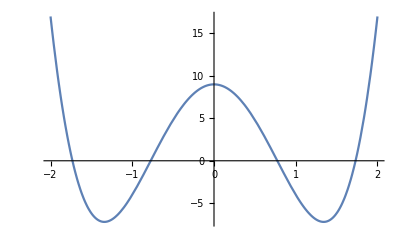

```mathematica
F=(x^2-3)(5 x^2-3)//Expand
Integrate[%,x]
Plot[F,{x,-2,2}]
```

#### gr. 1I

Zad. 1

```mathematica
f=4 x^3-5/x^10+3/((x^3)^(1/4));
g=ArcSin[x]/Tan[x];
h=Log[x]Cos[Sin[x]] ;
D[f,x]//Simplify
D[g,x]
D[h,x]
```

50/x^11+12 x^2-(9 (x^3)^(3/4))/(4 x^4)

Cot[x]/(√(1-x^2))-ArcSin[x] Csc[x]^2

Cos[Sin[x]]/x-Cos[x] Log[x] Sin[Sin[x]]

Zad. 2

```mathematica
expr=x/(2-x);
Series[expr,{x,1,2}]
Normal[%]//Expand
%/.{x->0.9}
expr/.{x->0.9}
```

1+2 (x-1)+2 (x-1)^2+O[x-1]^3

1-2 x+2 x^2

0.82

0.818182

Zad. 3

```mathematica
(4x+3)(x^2-4)//Expand
Integrate[%,x]
Solve[D[%,x]==0,x]
```

-12-16 x+3 x^2+4 x^3

-12 x-8 x^2+x^3+x^4

{{x→-2},{x→-3/4},{x→2}}